```mathematica
RAW DATA  



100
```

```mathematica
angr={0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,230,240,250,260,270,280,290,300,310,320,330,340,350};
intr={ 5657,5972,5860,5570,5064,4377,3401,2636,1896,1381,1119,1138,1417,2037,2710,3607,4398,4197,3376,2520,      1820,1345,1155,1153,1447,2055,2775,3608,4520,5213};
ar=Transpose@{angr,intr};
```

```mathematica
ListPlot[ar,PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle [°]", " Intensity [counts]"} ,PlotRange->{{0,360}, {990,6200}}]
```

-Graphics-

```mathematica
abr=NonlinearModelFit[ar, c+h*(Sin [f(x+d)])^2 ,{{h,5860},{d,75},{c,1000},{f,0.0172}},x]
```

FittedModel[1071.83+4872.17 Sin[0.01753 (75.0053+x)]^2]

```mathematica
abr["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
h | 4872.17 | 21.2551 | 229.224 | 1.64243×10^-44
d | 75.0053 | 0.311985 | 240.413 | 4.75971×10^-45
c | 1071.83 | 11.2331 | 95.4178 | 1.25615×10^-34
f | 0.01753 | 0.0000195119 | 898.426 | 6.22608×10^-60

```mathematica
abr["AdjustedRSquared"]
```

0.999884

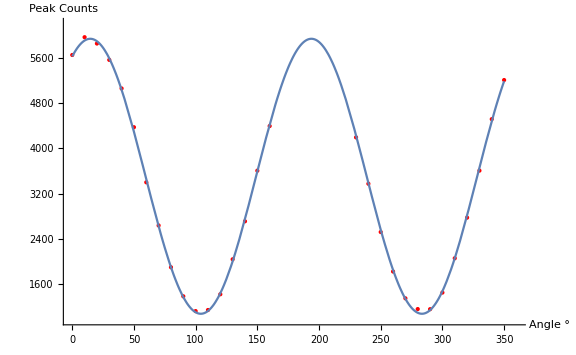

```mathematica
abcd=Show[ListPlot[ar, PlotStyle->Directive[Thin,PointSize[Large],Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle  °", " Peak Counts"} ],Plot[{c+h*( Sin[f (x+d)])^2}/.{h->4872.174680020012,f->0.017529964224497756,d->75.00528473912236,c->1071.8340427628978},{x,0,350}],PlotRange->{{0,360}, {980,6200}}]
```

```mathematica
111
```

```mathematica
bangr={18,180,198,216,234,252,270,288,306,324,312,360};
bintr={ 1704,2002,1920,1743,1449,1253,1190,1226,1385,1533,1737,2260};
br=Transpose@{bangr,bintr};
```

```mathematica
ListPlot[br,PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle [°]", " Intensity [counts]"} ,PlotRange->{{0,370}, {1000,2600}}]
```

-Graphics-

```mathematica
lr=LinearModelFit[br,{1},x]
```

FittedModel[1616.83]

```mathematica
lr["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1616.83 | 97.2398 | 16.6273 | 3.83682×10^-9

```mathematica
lr["AdjustedRSquared"]
```

0.

```mathematica
abbr=NonlinearModelFit[br, c+h*(Sin [f(x+d)])^2 ,{{h,5860},{d,75},{c,1000},{f,0.0172}},x]
```

FittedModel[1177.62+947.539 Sin[0.015761 (128.747+x)]^2]

```mathematica
abbr["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
h | 947.539 | 110.105 | 8.60574 | 0.0000257276
d | 128.747 | 15.2225 | 8.45766 | 0.0000291956
c | 1177.62 | 63.5548 | 18.5292 | 7.41902×10^-8
f | 0.015761 | 0.000635397 | 24.8049 | 7.45965×10^-9

```mathematica
abr["AdjustedRSquared"]
```

0.999884

```mathematica
abbrf=Show[ListPlot[br, PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle  °", " Peak Counts"} ],Plot[{c+h*( Sin[f (x+d)])^2}/.{h->947.5386326381642,f->0.015760964489861116,d->128.74658794362796,c->1177.6200367074168},{x,180,350}],Plot[{1616},{x,180,350}],PlotRange->{{170,360}, {980,4000}}]
```

-Graphics-

```mathematica
FITTED DATA  



100
```

```mathematica
ang={0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,230,240,250,260,270,280,290,300,310,320,330,340,350};
int={ 5676.9,5897.97,5899.53,5555.95,5076.54,4331.27,3410.16,2680.16,1884,1368.24,1119.0000000000,1138.0000000,1417.0000000,2013.57,2744.28,3594.18,4407.16,4179.69,3310.45,2501.92,      1788.51,1318.09,1155.000000000,1132.63,1429.52,2052.17,2777.99,3612.04,4519.06,5126.59};
a=Transpose@{ang,int};
ListPlot[a ,PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle [°]", " Intensity [counts]"} ,PlotRange->{{0,360}, {990,6200}}]
```

-Graphics-

```mathematica
ab=NonlinearModelFit[a, c+h*(Sin [f(x+d)])^2 ,{{h,5860},{d,75},{c,1000},{f,0.0172}},x]
```

FittedModel[1064.3+4862.8 Sin[0.0175385 (74.9283+x)]^2]

```mathematica
ab["AdjustedRSquared"]
```

0.999869

```mathematica
ab["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
h | 4862.8 | 22.4678 | 216.434 | 7.30195×10^-44
d | 74.9283 | 0.33027 | 226.87 | 2.14778×10^-44
c | 1064.3 | 11.8795 | 89.5909 | 6.4337×10^-34
f | 0.0175385 | 0.0000206779 | 848.18 | 2.78004×10^-59

```mathematica
Sqrt[4862.80191632002]
```

69.7338

```mathematica
abcp=Show[ListPlot[a, PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle  °", " Peak Counts"} ],Plot[{c+h*( Sin[f (x+d)])^2}/.{h->4862.80191632002,f->0.01753854337347679,d->74.92825228669514,c->1064.2965669948264},{x,0,350}]]
```

-Graphics-

```mathematica
111
```

```mathematica
bang={180,198,216,234,252,270,288,306,324,312,360};
bint={ 1980.43,1908.34,1684.74,1488.55,1240.36,1180.63,1228.42,1352.21,1528.02,1684.01,2214.73};
b=Transpose@{bang,bint};
ListPlot[b,PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle [°]", " Intensity [counts]"} ,PlotRange->{{150,370}, {1000,2600}}]
```

-Graphics-

```mathematica
ab=NonlinearModelFit[b, c+h*(Sin [f(x+d)])^2 ,{{h,5860},{d,75},{c,1000},{f,0.0172}},x]
```

FittedModel[1191.59+981.932 Sin[0.0142438 (171.327+x)]^2]

```mathematica
ab["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
h | 981.932 | 199.947 | 4.91096 | 0.00173137
d | 171.327 | 97.4357 | 1.75836 | 0.122095
c | 1191.59 | 69.516 | 17.1412 | 5.64502×10^-7
f | 0.0142438 | 0.00314637 | 4.52707 | 0.00270916

```mathematica
ab["AdjustedRSquared"]
```

0.995109

```mathematica
Sqrt[981.9316152749175]
```

31.3358

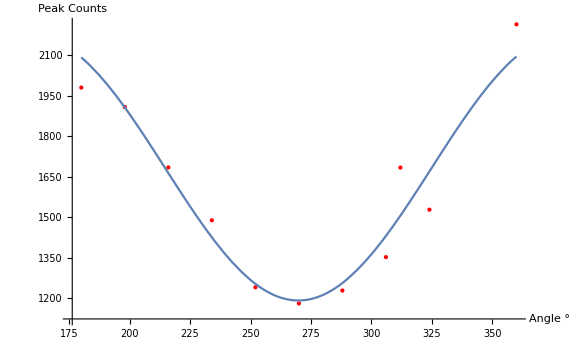

```mathematica
abff=Show[ListPlot[b, PlotStyle->Directive[Thin,PointSize[Large],Red,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle  °", " Peak Counts"} ],Plot[{c+h*( Sin[f (x+d)])^2}/.{h->981.9316152749175,f->0.014243849822070413,d->171.32662784697084,c->1191.5878897026141},{x,180,360}]]
```

```mathematica
Show[abff,abcp, PlotRange->{{0,365}, {500,6200}}]
```

-Graphics-

```mathematica
Show[abff,abcp, PlotRange->{{170,365}, {1000,6200}}]
```

-Graphics-

```mathematica
|
```

```mathematica
sl={            0,      201,     300    ,   400,     500,   600,    700          ,800,     900,         1000,       1200, 1300};
peak={  3121  , 4817 , 5325 ,   6640,  7772,  8859,   10765  , 13502, 15068,    15464,    16994,18080};
a=Transpose@{sl,peak};
ListPlot[a ,PlotStyle->Directive[Thin,PointSize[Large],Green,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle [°]", " Intensity [counts]"} ]
```

-Graphics-

```mathematica
FindFit[a, c*x +d,{c,d},x]
```

{c→12.6983,d→2173.16}

```mathematica
LinearModelFit[a,x,x]
```

FittedModel[2173.16+12.6983 x]

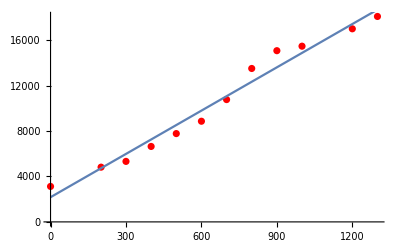

```mathematica
Show[ListPlot[a,PlotStyle->Red],Plot[%13[x],{x,0,1300}]]
```

```mathematica
NonlinearModelFit[a, c+x* b*Sin [x],{c,b},x]
```

FittedModel[10294.5+2.61097 x Sin[x]]

```mathematica
%48["AdjustedRSquared"]
```

0.798258

```mathematica
%48["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 10294.5 | 1534.64 | 6.7081 | 0.0000531088
b | 2.61097 | 3.07506 | 0.849081 | 0.4157

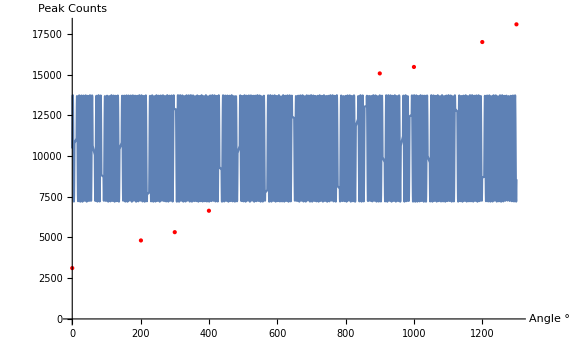

```mathematica
Show[ListPlot[a, PlotStyle->Directive[Thin,PointSize[Large],Red,"LineColor"->Red,AbsoluteThickness[1]], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]] ,
 AxesLabel->{" Angle  °", " Peak Counts"} ],Plot[{ c+ b*Sin [x]}/.{b->3263.9684322705243,c->10463.82931894083},{x,0,1300}]]
```